```mathematica
Get["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\Mathematica\\CDTFunctions.wl"]
```

```mathematica
groundTruth = VPCounts[16,4];
groundTruth=KeySortBy[groundTruth,groundTruth[#]&];
groundTruthNorm=groundTruth/Total[groundTruth];
order = Keys[groundTruth];
```

```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data";
files=FileNames["Statistical_Volume_16_TimeSize_4*.csv",folder];
vpData = LoadVPData[files];
```

```mathematica
order = Keys[Counts[vpData[1][[1]]]];
```

```mathematica
vpCountsNormed =Association[Table[stepCount-> Table[SortNormCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

```mathematica
vpCounts =Association[Table[stepCount-> Table[SortCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

```mathematica
vpCountsScaled =Association[Table[stepCount-> Table[Total[groundTruth]SortNormCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

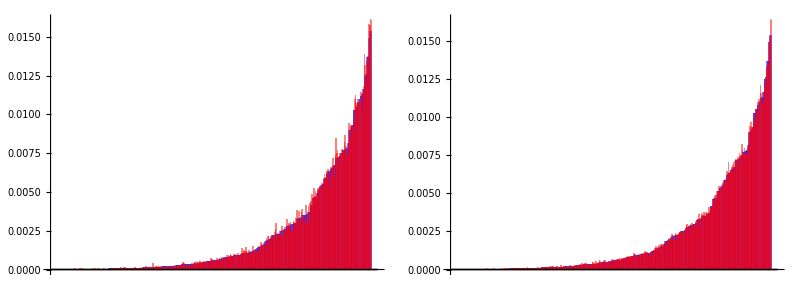

```mathematica
Grid[{{Show[{BarChart[groundTruthNorm,ChartStyle->Directive[Opacity[.5],Blue]],BarChart[vpCountsNormed[1][[1]],ChartStyle->Directive[Opacity[.5],Red]]}],Show[{BarChart[groundTruthNorm,ChartStyle->Directive[Opacity[.5],Blue]],BarChart[vpCountsNormed[9][[1]],ChartStyle->Directive[Opacity[.5],Red]]}]}}]
```

```mathematica
Similarity[statisticalData_,orderedAnalCounts_]:=Module[{s1,s2},
{s1,s2} = KeyIntersection[{statisticalData,orderedAnalCounts}];
1-Median[Abs[N[Values[(s1-s2)/s2]]]]]
```

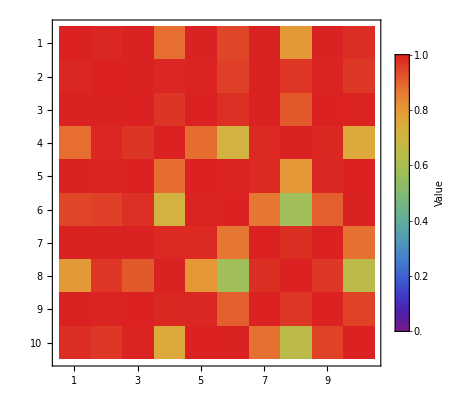
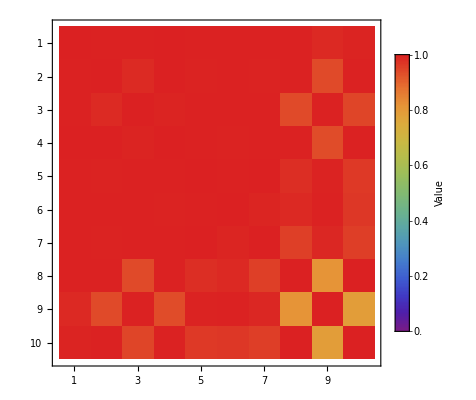
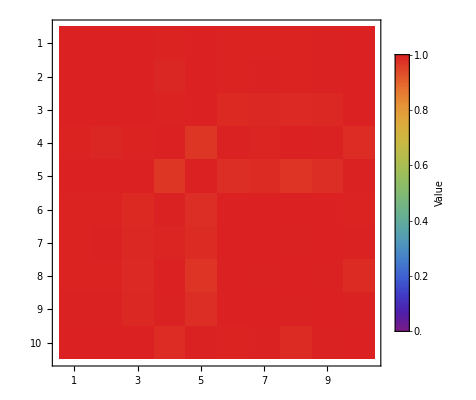
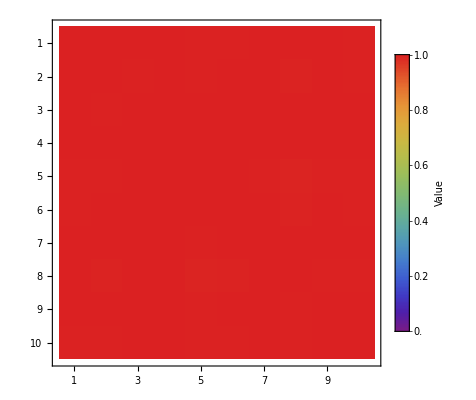
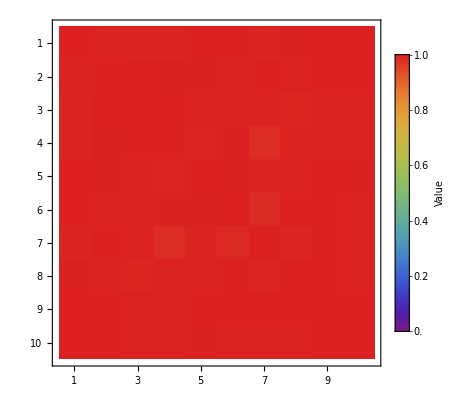
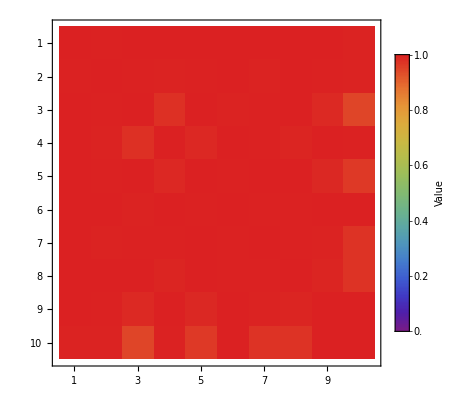
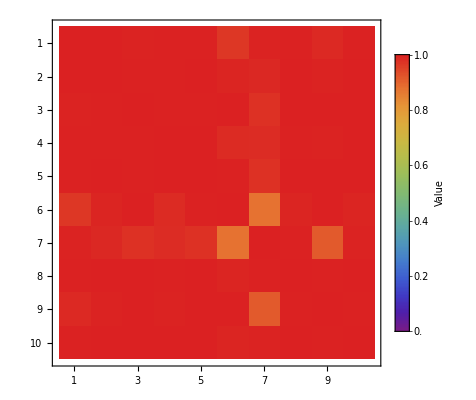
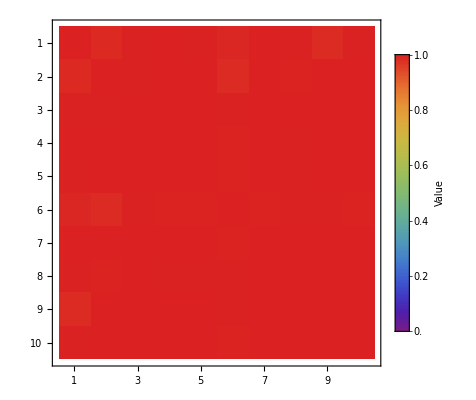
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{Table[MatrixPlot[Table[DistributionFitTest[Values[vpCounts[s][[i]]],Values[vpCounts[s][[j]]]],{i,10},{j,10}],ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][Clip[#,{0,1}]/1]&),{0,1}},LegendLabel->"Value"],Right]
,ColorFunction->(ColorData["Rainbow"][Clip[#,{0,1}]/1]&)],{s,9}]}]
```

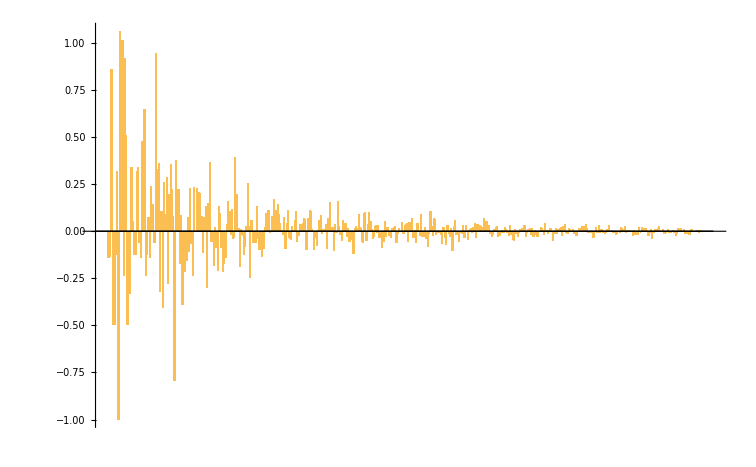

```mathematica
BarChart[(Mean[vpCountsScaled[9]]-groundTruth)/groundTruth]
```